# Unit 3 - Lists, Equations, and Rules

Topics covered in this unit are listed below.

Lists

Tasting the power of lists

Operations on lists

Selecting elements of a list

Solving Equations

Rules

Tricks and good practice

## Lists

Lists are central constructs in Mathematica. Without lists, many tasks would require programming Mathematica. Properly using lists can remarkably improve the performance of computing because less code and less computing time are needed.

A list is a data structure storing a collection of all kinds of objects. It is used to represent a set, an array, a vector, a matrix, or a sequences. Most Mathematica built-in functions can directly operate on lists.

We can directly create a list by using curly braces { }. For example,

```mathematica
list1={2, 3, 5, 7, 11};
```

is a list containing 5 elements, i.e., 2, 3, 4, 7, 11. Because a list itself is a kind of data value, a list can be embedded in another list. For example,

```mathematica
list2={2, 3, {5, {7}, 9}};
```

is also a valid list.

Other examples of lists can be, to name a few,

```mathematica
list3={x^2-2x+3,2 x^3-5Sin[x],1};
list4={2x+3y==0,3x-5y==1};
list5={x+3y-4z==-1,2x-3y+z==2,5x+3z==8};
list6={Plot[Sin[x],{x,-Pi,Pi}], Plot[Cos[2x],{x,-Pi,2Pi}]};
```

We can also use Range, Table, or NestList to create lists more efficiently if there is a formula for data values in a list.

Range

Usage:

Range[n], generating a list {1, 2, ⋯, n}, where n is a positive integer.

Range[i_min,i_max], generating a list {i_min,i_min+1,i_min+2,⋯,i_max}.

Range[i_min,i_max,di], generating a list {i_min,i_min+di,i_min+2di,i_min+3di,⋯,i_max}, where di is called the step or step size.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[1,10,1]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[1,10,2]
```

{1,3,5,7,9}

Table

Usage:

Table[expr,{i_max}], generating a list of i_max copies of the value of expr.

Table[expr,{i,i_min,i_max}], generating a list of the values of expr when i runs from i_min to i_max.

Table[expr,{i,i_max}], the same as Table[expr,{i,1,i_max}]

Table[expr,{i,i_min,i_max,di}], generating a list of the values of expr when i runs from i_min to i_max with step size di.

Table[expr,{i,{a_1,a_2, a_3,⋯}}], generating a list of the values of expr when i takes values a_1,a_2, a_3,⋯.

Table[expr,{i,⋯},{j,⋯},…], generating a list of the values of expr when i, j, ⋯ take their corresponding values.

```mathematica
Clear[a,b]
Table[a+2b, {5}]
```

{a+2 b,a+2 b,a+2 b,a+2 b,a+2 b}

```mathematica
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[2i-1,{i,10}]
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
Clear[x]
Table[Sin[i*x],{i,1,10,2}]
```

{Sin[x],Sin[3 x],Sin[5 x],Sin[7 x],Sin[9 x]}

```mathematica
Clear[x]
Table[Sin[(i*π)/2*x],{i,{1,2,5,7,20}}]
```

{Sin[(π x)/2],Sin[π x],Sin[(5 π x)/2],Sin[(7 π x)/2],Sin[10 π x]}

```mathematica
Table[RandomInteger[{1,100}],{i,10}] (* giving a list of 10 random integers in the range from 1 to 100 *)
```

{61,42,74,94,74,49,67,85,45,43}

```mathematica
Table[Prime[i],{i,20}](* Prime[i] gives the ith prime number *)
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
Clear[x]
Table[i*x+j*y,{i,3},{j,{1,3,7}}]
```

{{x+y,x+3 y,x+7 y},{2 x+y,2 x+3 y,2 x+7 y},{3 x+y,3 x+3 y,3 x+7 y}}

```mathematica
%//MatrixForm
```

(x+y | x+3 y | x+7 y
2 x+y | 2 x+3 y | 2 x+7 y
3 x+y | 3 x+3 y | 3 x+7 y)

NestList

Usage: NestList[f,expr,n], generating a list of the results of applying the function f to expr 0 through n times.

Note: When defining f(x), we must know that both x and f(x) have very special meanings - While x denotes the value of “previous” term, f(x) gives the value of present term.

To generate the sequence of 2, 4, 8, 16, 32, ⋯, 1024, we can run the following commands.

```mathematica
f[x_]:=2x(* how about 2^x ? *)
NestList[f, 1, 10]
```

{1,2,4,8,16,32,64,128,256,512,1024}

We may use anonymous function as follows.

```mathematica
NestList[2#1&,1,10]
```

{1,2,4,8,16,32,64,128,256,512,1024}

## Tasting the power of lists

Most Mathematica functions can take lists as their arguments. Remember that basic algebraic operators like +,-,×,/ and ^ are all built-in Mathematica functions. When a function is applied to a list, it is applied to each element of the list, and returns a list of corresponding results.

```mathematica
3{1,2,3}
```

{3,6,9}

```mathematica
1/{1,2,3}
```

{1,1/2,1/3}

```mathematica
2+{1,2,3}
```

{3,4,5}

```mathematica
{1,2,3}+{2,4,6}
```

{3,6,9}

```mathematica
{1,2,3}*{2,4,6}
```

{2,8,18}

```mathematica
{1,2,3}/{2,4,6}
```

{1/2,1/2,1/2}

```mathematica
{1,2,3}^2
```

{1,4,9}

```mathematica
2^{1,2,3}
```

{2,4,8}

```mathematica
{1,2,3}^{2,4,6}
```

{1,16,729}

```mathematica
Sin[{0,Pi/6,Pi/3,Pi/2,Pi}]
```

{0,1/2,(√3)/2,1,0}

Moreover, user-defined functions may also take lists as arguments. For example,

```mathematica
f[x_]:=x^2+2x+1
```

```mathematica
f[1]
```

4

```mathematica
f[2]
```

9

```mathematica
f[{1,2,1}]
```

{4,9,4}

## Operations on lists

Accessing elements of a list

```mathematica
x=Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
x[[1]]
```

1

```mathematica
x[[{2,3,5}]]
```

{4,9,25}

```mathematica
x[[2;;8]](* same as x[[Range[2,8]]] *)
```

{4,9,16,25,36,49,64}

```mathematica
First[x]
```

1

```mathematica
Last[x]
```

100

```mathematica
100
```

100

```mathematica
Rest[x] (* all but the first element *)
```

{4,9,16,25,36,49,64,81,100}

```mathematica
x[[2;;]] (* same as Rest[x] *)
```

{4,9,16,25,36,49,64,81,100}

```mathematica
x[[3;;]] (* same as Rest[Rest[x]] *)
```

{9,16,25,36,49,64,81,100}

```mathematica
x[[;;-2]] (* -1 indicates the last entry *)
```

{1,4,9,16,25,36,49,64,81}

```mathematica
x[[;;-3]]
```

{1,4,9,16,25,36,49,64}

```mathematica
matrix=Table[Table[RandomInteger[{0,10}],{2}],{5}]
```

{{8,7},{3,5},{2,0},{9,1},{8,1}}

```mathematica
matrix//MatrixForm
```

(8 | 7
3 | 5
2 | 0
9 | 1
8 | 1)

```mathematica
matrix[[3]] (* 3rd row, same as matrxi[[3,;;]] or matrix[[3,All]] *)
```

{2,0}

```mathematica
matrix[[;;,2]] (* 2nd column, same as matrix[[All,2]] *)
```

{7,5,0,1,1}

```mathematica
matrix[[2;;4,2]]  (* 2nd through 4th entries on 2nd column *)
```

{5,0,1}

Some basic functions

ListQ, determining if an object is a list or not.

```mathematica
ListQ[5]
```

False

```mathematica
ListQ[{5,3, {1,{2}}}]
```

True

MemberQ, determining if an object is a member of a list

```mathematica
MemberQ[{1,2,3,4,5},3]
```

True

```mathematica
MemberQ[{1,2,3,{4,{5}}},5]
```

False

```mathematica
MemberQ[Flatten[{1,2,3,{4,{5}}}],5]
```

True

```mathematica
MemberQ[{1,2,3,{4,{5}}},5,3] (* test bu the 3rd level *)
```

True

Length, giving the size of a list.

```mathematica
x=Range[10]
Length[x]
```

{1,2,3,4,5,6,7,8,9,10}

10

```mathematica
x={1,2,3,{4,5,6, {7}}};
Length[x]
```

4

Flatten, removing inner curly braces.

1. Flatten[list], flattening out nested lists.
2. Flatten[list,n], flattening out nested lists to level n.
    For other usages, refer to the Wolfram Documentation.

```mathematica
x={{{1,2},{2,3}},{{4,5},{6, {7}}}};
Flatten[x]
```

{1,2,2,3,4,5,6,7}

```mathematica
Flatten[x,1]
```

{{1,2},{2,3},{4,5},{6,{7}}}

Map, applying a function to each element of a list on the first level.

Usage: Map[f,expr], applying the function f  to each element on the first level in expr.

```mathematica
f[x_]:=x^2
Map[f,{1,2,3,4,5}]
```

{1,4,9,16,25}

```mathematica
Map[Flatten,{{1,2},{3,4,{5}},{6,{7,{8,{9,{10}}}}}}]
```

{{1,2},{3,4,5},{6,7,8,9,10}}

```mathematica
f[{x_,y_}]:=y(* extract the second element of each pair *)
Map[f,{{1,2},{3,4},{5,6},{7,8}}]
```

{2,4,6,8}

Example 1
Use Table to create a list of pairs {x,y}, where x and y assume values from the lists {1/11,2/11,...,5/11} and {1/13,3/13,7/13}, respectively. Then, use Map to create a list of {x,y,x×y}.

```mathematica
Table[{x/11,y/13},{x,1,5},{y,{1,3,7}}]
```

{{{1/11,1/13},{1/11,3/13},{1/11,7/13}},{{2/11,1/13},{2/11,3/13},{2/11,7/13}},{{3/11,1/13},{3/11,3/13},{3/11,7/13}},{{4/11,1/13},{4/11,3/13},{4/11,7/13}},{{5/11,1/13},{5/11,3/13},{5/11,7/13}}}

```mathematica
x=Flatten[%,1]
```

{{1/11,1/13},{1/11,3/13},{1/11,7/13},{2/11,1/13},{2/11,3/13},{2/11,7/13},{3/11,1/13},{3/11,3/13},{3/11,7/13},{4/11,1/13},{4/11,3/13},{4/11,7/13},{5/11,1/13},{5/11,3/13},{5/11,7/13}}

```mathematica
f[{x_,y_}]:={x,y,x*y};
Map[f,x]
```

{{1/11,1/13,1/143},{1/11,3/13,3/143},{1/11,7/13,7/143},{2/11,1/13,2/143},{2/11,3/13,6/143},{2/11,7/13,14/143},{3/11,1/13,3/143},{3/11,3/13,9/143},{3/11,7/13,21/143},{4/11,1/13,4/143},{4/11,3/13,12/143},{4/11,7/13,28/143},{5/11,1/13,5/143},{5/11,3/13,15/143},{5/11,7/13,35/143}}

Apply, passing elements of a list on the first level to a function

Usage: Apply[f,{a_1,a_2,a_3,⋯,a_n}], equivalent to f[a_1,a_2,a_3,⋯,a_n].

```mathematica
x=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Plus[x](* Plus does not take a list as its arguments *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Apply[Plus,x]
```

55

```mathematica
Times[x]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Apply[Times,x]
```

3628800

Partition, partitioning basically a list into non-overlapping sublists of specified length.

```mathematica
Partition[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},4]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}

```mathematica
Partition[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},4]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12}}

```mathematica
Grid[Partition[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},4],Frame->All]
```

1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16

Other basic functions include Append, Prepend, Union, and Join. Refer to the Wolfram Documentation.

## Selecting elements of a list

Usage:

Select[list,crit], picking out all elements e_i of list for which crit[e_i] is true.

Select[list,crit,n], picking out the first n elements e_i of list for which crit[e_i] is true.

```mathematica
Select[{1,2,3,4,5,6,7,8},EvenQ]
```

{2,4,6,8}

```mathematica
Select[{1,2,3,4,5,6,7,8},OddQ,3]
```

{1,3,5}

```mathematica
Select[{-1.1795,0.5897-1.7445 ⅈ,0.5897+1.7445 ⅈ, 1.2345},# ∈ Reals&](* all real numbers *)
```

{-1.1795,1.2345}

We may use logical connectives && (and), || (or), ! (not) to create more complicated conditions. In a conditional expression, the order of evaluation is as follows.
First, evaluate algebraic expressions.
Second, evaluate relational expressions. E.g., x>4, x^2-3x+1==0.
Lastly, evaluate logical expressions. In this step, ! is evaluated before && and ||.

Parentheses ( ) can be used to change the order of computation.

Both MATH 200 and MATH 250 cover the contents on symbolic logic.

```mathematica
Select[{1,2,3,4,5,6,7,8},5≤#<8&](* pure function; see Unit 2 *)
```

{5,6,7}

```mathematica
Select[{1,2,3,4,5,6,7,8},5≤#<8&&EvenQ[#]&]
```

{6}

```mathematica
Select[{1,2,3,4,5,6,7,8},5≤#<8&&!EvenQ[#]&] (* !EqualQ[x] is equivalent to OddQ[x] *)
```

{5,7}

```mathematica
Select[{1,2,3,4,5,6,7,8},Mod[#,3]==0&](* divisible by 3 *)
```

{3,6}

```mathematica
Select[{1,2,3,4,5,6,7,8},Mod[#,3]==0||Mod[#,4]==0&] (* divisible by either 3 or 4 *)
```

{3,4,6,8}

```mathematica
Select[{1,2,3,4,5,6,7,8},!(Mod[#,3]==0||Mod[#,4]==0)&] (* all but those divisible by either 3 or 4 *)
```

{1,2,5,7}

Some commonly used “tools”

Total, calculating the total of a list

```mathematica
Total[{1,2,3,4}] (* find the sum of a data set *)
```

10

Mean,finding the statistical mean of the elements in a list

```mathematica
Mean[{1,2,3,4}] (* find the mean value of a data set *)
```

5/2

Max, giving the numerically largest element in a list

```mathematica
Max[{1,2,3,4}] (* find the maximum value in a data set *)
```

4

Min,giving the numerically smallest element in a list

```mathematica
Min[{1,2,3,4}] (* find the minimum value in a data set *)
```

1

Sort, sorting the elements of a list into canonical order

```mathematica
Sort[{3,2,1,4}] (* sort the data set into canonical order *)
```

{1,2,3,4}

```mathematica
Sort[{d,b,c,a}]
```

{a,b,c,d}

```mathematica
Sort[{"We","You","I","They"}]
```

{I,They,We,You}

## Solving Equations

Mathematica is able to solve various types of equations. Double equal signs are used to construct an equation.

It is double equal signs == when we input an equation in Mathematica. Using a single equal sign = is a common mistake for it is reserved for assignment rather than a logical test.

```mathematica
1=2-1;(* not a Mathematica equation *)
```

Set::setraw: Cannot assign to raw object 1.

```mathematica
Clear[x]
x^2-3x+4=0 ;(* not a Mathematica equation *)
```

Set::write: Tag Plus in 4 - 3\ x + x^2 is Protected.

Mathematica provides three functions for solving ordinary equations. They are Solve, NSolve, and FindRoot.

Solve

Usage:

Solve[expr,vars], solving the system expr of equations or inequalities for the variables vars.

Solve[expr,vars, domain], solving over the domain. Common choices of domain are Reals, Integers, and Complexes.

```mathematica
Clear[x];
Solve[(x^2-3x+3)(x-2)(x-1.5)==0,x]//N (* equivalent to Solve[⋯,x,Complexes]*)
```

{{x→1.5},{x→1.5-0.866025 ⅈ},{x→1.5+0.866025 ⅈ},{x→2.}}

```mathematica
Solve[(x^2-3x+3)(x-2)(x-1.5)==0,x,Reals]//N
```

{{x→1.5},{x→2.}}

```mathematica
Solve[1/2(x^2-3x+3)(x-2)(2x-3)==0,x,Integers]
```

{{x→2}}

Now, let us solve a system of equations. We may construct a list consisting of all equations in a system as shown below.

```mathematica
Clear[x,y]
Solve[{2x-3y==1,3x+5y==6},{x,y}]
```

{{x→23/19,y→9/19}}

We can also use the operator &&, which is the logic connective AND, to combine all equations in a system into a single expression.

```mathematica
Solve[2x-3y==1&&3x+5y==6,{x,y}]
```

{{x→23/19,y→9/19}}

```mathematica
Clear[x,y,z]
Solve[{2x-3y+z==1,3x+5y-3z==6,2x+4z==-1},{x,y,z}]
```

{{x→22/21,y→3/28,z→-65/84}}

```mathematica
Solve[{2x-3y+z==1,3x+5y-3z==6,6x+10y-6z==-1},{x,y,z}](* the system is inconsistent ! *)
```

{}

We can specify on which interval to find solutions.

```mathematica
Solve[(x-1)(x-2)(x-3)==0&&1≤x≤2,x]
```

{{x→1},{x→2}}

NSolve

It seems that NSolve[⋯] is equivalent to N[Solve[⋯]]. But it is not. While Solve attempts to find an exact solution, NSolve tries to find a numerical approximation to the exact solution.

NSolve and Solve have similar usage.

```mathematica
NSolve[(x^2-3x+3)(x-2)(x-1.5)==0,x]
```

{{x→1.5},{x→1.5-0.866025 ⅈ},{x→1.5+0.866025 ⅈ},{x→2.}}

```mathematica
NSolve[(x^2-3x+3)(x-2)(x-1.5)==0,x,Reals]
```

{{x→1.5},{x→2.}}

```mathematica
NSolve[{2x-3y==1,3x+5y==6},{x,y}]
```

{{x→1.21053,y→0.473684}}

```mathematica
NSolve[(x-1)(x-2)(x-3)==0&&1≤x≤2,x]
```

{{x→1.},{x→2.}}

Tips: Solving equations involving periodical functions, we had better specify the range on which we find solutions. For example,

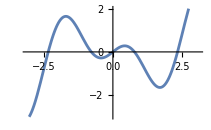

{-2.35619,-0.785398,0.,0.785398,2.35619}

```mathematica
f[x_]:=x Cos[2x]
Plot[f[x],{x,-Pi,Pi},PlotRange->{-3,2}]
x/.NSolve[{f[x]==0,-Pi<=x<=Pi},x]
```

The following examples help us discover the difference between Solve and NSolve.

```mathematica
Solve[(2x^3+4x-1)(x^2+1)==0,x]
```

{{x→-ⅈ},{x→ⅈ},{x→(9+√465)^(1/3)/6^(2/3)-(2 2^(2/3))/(3 (9+√465))^(1/3)},{x→-((1+ⅈ √3) (9+√465)^(1/3))/(2 6^(2/3))+(2^(2/3) (1-ⅈ √3))/(3 (9+√465))^(1/3)},{x→-((1-ⅈ √3) (9+√465)^(1/3))/(2 6^(2/3))+(2^(2/3) (1+ⅈ √3))/(3 (9+√465))^(1/3)}}

```mathematica
Solve[3 x^6+4x+1==0,x]
```

{{x→-1},{x→Root[1+3 #1-3 #1^2+3 #1^3-3 #1^4+3 #1^5&,1]},{x→Root[1+3 #1-3 #1^2+3 #1^3-3 #1^4+3 #1^5&,2]},{x→Root[1+3 #1-3 #1^2+3 #1^3-3 #1^4+3 #1^5&,3]},{x→Root[1+3 #1-3 #1^2+3 #1^3-3 #1^4+3 #1^5&,4]},{x→Root[1+3 #1-3 #1^2+3 #1^3-3 #1^4+3 #1^5&,5]}}

It is proved that there is no general formula for solving polynomial equation of degree 5 and higher. If the equation cannot be factored over integer or rational numbers, possibly by applying rational zero test, Mathematica just simply gives “results” like this one. In this situation, NSolve is a better choice.

```mathematica
NSolve[3 x^6+4x+1==0,x]
```

{{x→-1.},{x→-0.276651-1.01469 ⅈ},{x→-0.276651+1.01469 ⅈ},{x→-0.250184},{x→0.901743-0.625599 ⅈ},{x→0.901743+0.625599 ⅈ}}

FindRoot

Basic usage: FindRoot[eqn, {x,x_0}], searching for a numerical solution of eqn starting from an initial guess x=x_0.

We usually first plot the involved function(s), and determine an initial guess according to the graph.

FindRoot attempts to find one numerical solution at a time. If there are multiple solutions, we shall apply the function multiple times with different initial guesses.

Example 2
Find the roots of the polynomial function y=x^2-3x+1.

We first plot the graph of the function. Then, according to the graph, we apply FindRoot once for each x-intercept, i.e., a root. A initial guess of a root can be any value that, you believe, is close to the corresponding x-intercept.

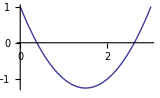

```mathematica
Plot[x^2-3x+1,{x,0,3},ImageSize->160]
```

```mathematica
FindRoot[x^2-3x+1==0,{x,0.5}]
```

{x→0.381966}

```mathematica
FindRoot[x^2-3x+1==0,{x,2.5}]
```

{x→2.61803}

Example 3
Find the point where y=sin x and y=2x+1 intersect each other.

We can take the approach shown in Example 2, if we change the problem to finding the roots of y=sin x-(2x+1). But let us take a different approach. We first plot the two functions on a single figure. Then, make an initial guess of x coordinate of the point where the two curves intersect.

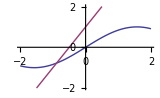

```mathematica
Plot[{Sin[x],2x+1},{x,-2,2},PlotRange->{-2,2},ImageSize->160]
```

```mathematica
FindRoot[Sin[x]==2x+1,{x,-1}]
```

{x→-0.887862}

```mathematica
{x,2x+1}/.% (* find the coordinates of the point *)
```

{-0.887862,-0.775724}

```mathematica
Print["The point is (", %[[1]], ", ", %[[2]], ")."]
```

The point is (-0.887862, -0.775724).

Example 4
Find a quadratic function that passes three points, (-1,2),(1,7), and (3,10).

Let f(x)=a x^2+b x+c be the function. For the three distinct points are on the curve of the function, we can setup a system of three equations in three unknown coefficients, a,b, and c, and have Mathematica find the coefficients for us.

```mathematica
Clear[a,b,c]
f[x_]:=a*x^2+b*x+c
coefs=Solve[{f[-1]==2,f[1]==7,f[3]==10},{a,b,c}][[1]]
```

{a→-1/4,b→5/2,c→19/4}

Thus, the quadratic function is

```mathematica
f[x]/.coefs//TraditionalForm
```

-x^2/4+(5 x)/2+19/4

## Rules

A rule looks like x → 1.25. It defines a replacement of a symbol, e.g., x, with the corresponding value, e.g., 1.25.

We have see examples of using Solve, NSolve, and FindRoot. The output of each one is a list of rules.

The command expr /. rule first replaces involved symbols in expr with corresponding values defined in rule (or a list of rules), and then evaluate expr.

```mathematica
Clear[x]
```

```mathematica
x/.x->1
```

1

```mathematica
x^2/.x->{1,2,3}
```

{1,4,9}

```mathematica
Total[x^2/.x->{1,2,3}]
```

14

```mathematica
2 x^2+3y-1/.{x->1,y->0}
```

1

```mathematica
{{1/3 x+2/3 y,(x+y)/2},Max[Abs[{x,y}]],Sqrt[x^2+y^2]}/.{x->1,y->-2}
```

{{-1,-1/2},2,√5}

Working with Solve, NSolve and FindRoot

```mathematica
Clear[x,y]
NSolve[(x^2-3x+3)(x-1)(x-1.5)==0,x]
```

{{x→1.},{x→1.5},{x→1.5-0.866025 ⅈ},{x→1.5+0.866025 ⅈ}}

```mathematica
x/.%
```

{1.,1.5,1.5-0.866025 ⅈ,1.5+0.866025 ⅈ}

```mathematica
xs=x/.NSolve[(x^2-3x+3)(x-1)(x-1.5)==0,x,Reals]
```

{1.,1.5}

```mathematica
Apply[Times,xs] (* find the product of all real roots *)
```

1.5

```mathematica
Apply[Plus,xs] (* find the sum of all real roots *)
```

2.5

```mathematica
{x,x^2+3 y^2,y}/.NSolve[{2x-3y==1,3x+5y==6},{x,y}]
```

{{1.21053,2.1385,0.473684}}

→ (Rule) or :>  (RuleDelayed) ?

The difference between the two is the same like that between = (Set ) and := (SetDelayed). See Unit 1.

To type the symbol :> in Mathematica Input mode, type : and > plus any third key.

```mathematica
{x,x,x,x,x}/.x->RandomInteger[{0,100}]
```

{80,80,80,80,80}

```mathematica
{x,x,x,x,x}/.x:>RandomInteger[{0,100}]
```

{96,77,85,74,56}

## Tricks and good practice

A Mathematica session refers to the time period of your using Mathematica from starting the software to exiting it.

The longer a Mathematica session is and the more work you have done in a session, the more weirdness Mathematica will give to you. For example, your code worked before, but it doesn’t work now, though you have made no change at all. One major reason is that the workspace of Mathematica is like a bow of spaghetti. It is messed up and needs to be cleared. In probably over 85% of situations like this, it immediately solves the problem by clearing first your symbols that appear in the code you are running or testing as follows.

```mathematica
Clear[x] (* clear symbol x *)
Clear[x,y,f] (* clear symbols x, y, and f *)
Clear[x1,x2,x3] (* clear symbols x1, x2, and x3 *)
Clear["x*"] (* clear all symbols starting with x *)
```

```mathematica
Clear["Global`*"] (* clear all user-defined symbols *)
```

Perhaps, the best practice is to start each of your new task with the command: Clear[“Global`*”].

If you are doing multiple computing tasks in one single Mathematica notebook and need to present the notebook as a formal report, a good approach could be this way:

1. Start with the command Clear[“Global`*”].
2. Taking advantage of the interactive environment of Mathematica, gradually input and test your commands in multiple cells, if necessary.
3. After successfully testing your code, merge sequentially as many cells into a single cell as possible so that a computing task just uses a smaller number of cells. In the final version of the computing task, we may add “;” after some commands so as to filter unnecessary outputs. Our work will look clean and succinct.

For example, the task of finding a parabola, y=a x^2+b x+c, passing through points (0,1),(-1,5), and (3,2) could be done at first as follows.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=a x^2+b x+c
```

```mathematica
Solve[{f[0]==1,f[-1]==5,f[3]==2},{a,b,c}]
```

{{a→13/12,b→-35/12,c→1}}

```mathematica
f[x]/.%
```

{1-(35 x)/12+(13 x^2)/12}

```mathematica
%[[1]]
```

1-(35 x)/12+(13 x^2)/12

```mathematica
%//TraditionalForm
```

(13 x^2)/12-(35 x)/12+1

Now, after debugging and testing all your work for the task, merge cells as much as possible.

```mathematica
Clear["Global`*"]
f[x_]:=a x^2+b x+c
Solve[{f[0]==1,f[-1]==5,f[3]==2},{a,b,c}];
f[x]/.%;
%[[1]] //TraditionalForm
```

(13 x^2)/12-(35 x)/12+1

When working on a (word) problem which is complicated to you, the right way is always to first figure out how to do it on paper. This should be a golden rule for most people. If we don’t know how to find a way out, how can we teach computer to do it? From Lab 3 on, many questions will require you to find a solution on paper at first. Here, by solution we mean a mathematical model, an algorithm, or the procedure by which we solve the problem, instead of the final result. You will also need a calculus textbook at hand if you are struggling with some basic concepts covered by a calculus course.

© 2015-2024 by David Wang, dwang@liberty.edu